```mathematica
Quit[];
```

# Extrapolate pk

```mathematica
PSL_mass00z0
```

Alejandro Aviles
avilescervantes@gmail.com

```mathematica
SetDirectory[NotebookDirectory[]];

inputfilepkl="PSL_mass00z0.txt";
outputfilepkl="PSL_mass00z0_ep.txt";
```

## import pk

0.00001

521.888

time = 0.00679 seconds

-7
InterpolatingFunction[{{9.91962 10  , 5001.89}}, <>]

9.91962×10^-7

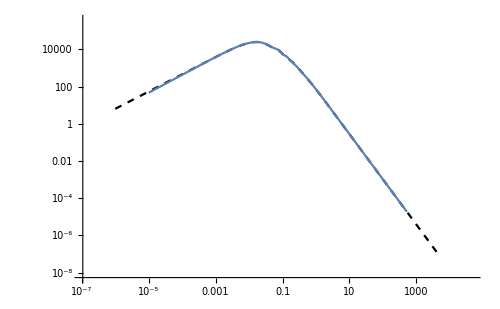

```mathematica
inputpkT=Import[inputfilepkl,"Table"];
kinMin=inputpkT[[1,1]]
kinMax=inputpkT[[-1,1]]
kcutmin=Max[0.001,kinMin];
kcutmax=Min[10,kinMax];

(*kcutmin=0.001;
kcutmax=2;*)


(*exagerando:*)
kmin=10^(-6); 
kmax=5000;


<<extrapolate.m
ta=AbsoluteTime[];
PSLT=ExtrapolatekLogLog[inputpkT,kcutmin,kmin,kcutmax,kmax];
Print["time = ",AbsoluteTime[]-ta," seconds"];
PSL=Interpolation[PSLT]

kInputMin=PSLT[[1,1]]
kInputMax=PSLT[[-1,1]];

LogLogPlot[PSL[k],{k,kinMin,kinMax}];


inputpk=Interpolation[inputpkT];
LogLogPlot[{inputpk[k]},{k,kinMin,kinMax}];
LogLogPlot[{PSL[k]},{k,kmin,kmax},PlotStyle->{Black,Dashed},ImageSize->500];
Show[%,%%]
```

```mathematica
Nkout=1000.;
d=Log[kmax/kmin]/(Nkout-1);
kTout=Table[kmin Exp[d*(i-1)],{i,1,Nkout}];
pkout=Table[{kTout[[i]],PSL[kTout[[i]]]},{i,1,Nkout}];
```

```mathematica
Export[outputfilepkl,pkout,"Table"]
```

PSL_mass00z0_ep.txt